# Single-atom in cavity LASER

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Clear["Global`*"]
```

```mathematica
Needs["Quantum`Notation`"];
```

```mathematica
SetQuantumAliases[];
```

### Three-level atom and up to two-photon restriction

## Defining Operators

```mathematica
DefineOperatorOnKets[Subscript[a, OverHat[1]],{|Subscript[0, OverHat[1]]⟩->0,Table[|Subscript[n, OverHat[1]]⟩ ->  √n|Subscript[(n-1), OverHat[1]]⟩,{n,1,2}]}//Flatten]
```

a_OverHat[1]·|0_OverHat[1]⟩→0
a_OverHat[1]·|1_OverHat[1]⟩→|0_OverHat[1]⟩
a_OverHat[1]·|2_OverHat[1]⟩→√2 |1_OverHat[1]⟩

```mathematica
DefineOperatorOnKets[SuperDagger[Subscript[a, OverHat[1]]], {Table[|Subscript[n, OverHat[1]]⟩ ->  √(n+1)|Subscript[(n+1), OverHat[1]]⟩,{n,0,1}],|Subscript[2, OverHat[1]]⟩->0}//Flatten]
```

a_OverHat[1]^†·|0_OverHat[1]⟩→|1_OverHat[1]⟩
a_OverHat[1]^†·|1_OverHat[1]⟩→√2 |2_OverHat[1]⟩
a_OverHat[1]^†·|2_OverHat[1]⟩→0

## Identification of Density Matrix Elements

```mathematica
Basis={|Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]⟩,|Subscript[0, OverHat[1]],Subscript[2, OverHat[2]]⟩,|Subscript[0, OverHat[1]],Subscript[3, OverHat[2]]⟩,|Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]⟩,|Subscript[1, OverHat[1]],Subscript[2, OverHat[2]]⟩,|Subscript[1, OverHat[1]],Subscript[3, OverHat[2]]⟩,|Subscript[2, OverHat[1]],Subscript[1, OverHat[2]]⟩,|Subscript[2, OverHat[1]],Subscript[2, OverHat[2]]⟩,|Subscript[2, OverHat[1]],Subscript[3, OverHat[2]]⟩};
```

```mathematica
BasisAdj={⟨Subscript[0, OverHat[1]],Subscript[1, OverHat[2]]|,⟨Subscript[0, OverHat[1]],Subscript[2, OverHat[2]]|,⟨Subscript[0, OverHat[1]],Subscript[3, OverHat[2]]|,⟨Subscript[1, OverHat[1]],Subscript[1, OverHat[2]]|,⟨Subscript[1, OverHat[1]],Subscript[2, OverHat[2]]|,⟨Subscript[1, OverHat[1]],Subscript[3, OverHat[2]]|,⟨Subscript[2, OverHat[1]],Subscript[1, OverHat[2]]|,⟨Subscript[2, OverHat[1]],Subscript[2, OverHat[2]]|,⟨Subscript[2, OverHat[1]],Subscript[3, OverHat[2]]|};
```

```mathematica
Calling=Table[Table[BasisAdj[[i]]·ρ̂[t]·Basis[[j]]-> ρ[i,j][t],{j,1,9}],{i,1,9}]//Flatten;
```

## Master Equation term by term

```mathematica
ρ̂'[1][t]=g·SuperDagger[Subscript[a, OverHat[1]]]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[2][t]=-g·|Subscript[2, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·Subscript[a, OverHat[1]]·ρ̂[t];
```

```mathematica
ρ̂'[3][t]=-g·ρ̂[t]·SuperDagger[Subscript[a, OverHat[1]]]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|;
```

```mathematica
ρ̂'[4][t]=g·ρ̂[t]·|Subscript[2, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·Subscript[a, OverHat[1]];
```

```mathematica
ρ̂'[5][t]=2·κ·Subscript[a, OverHat[1]]·ρ̂[t]·SuperDagger[Subscript[a, OverHat[1]]];
```

```mathematica
ρ̂'[6][t]=-κ·SuperDagger[Subscript[a, OverHat[1]]]·Subscript[a, OverHat[1]]·ρ̂[t];
```

```mathematica
ρ̂'[7][t]=-κ·ρ̂[t]·SuperDagger[Subscript[a, OverHat[1]]]·Subscript[a, OverHat[1]];
```

```mathematica
ρ̂'[8][t]=Γ/2·2·|Subscript[3, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·ρ̂[t]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|;
```

```mathematica
ρ̂'[9][t]=-Γ/2·|Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[10][t]=-Γ/2·ρ̂[t]·|Subscript[1, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|;
```

```mathematica
ρ̂'[11][t]=γ12/2·2·|Subscript[1, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[2, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|;
```

```mathematica
ρ̂'[12][t]=-γ12/2·|Subscript[2, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[13][t]=-γ12/2·ρ̂[t]·|Subscript[2, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|;
```

```mathematica
ρ̂'[14][t]=γ13/2·2·|Subscript[1, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[1, OverHat[2]]|;
```

```mathematica
ρ̂'[15][t]=-γ13/2·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[16][t]=-γ13/2·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|;
```

```mathematica
ρ̂'[17][t]=γ23/2·2·|Subscript[2, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[2, OverHat[2]]|;
```

```mathematica
ρ̂'[18][t]=-γ23/2·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|·ρ̂[t];
```

```mathematica
ρ̂'[19][t]=-γ23/2·ρ̂[t]·|Subscript[3, OverHat[2]]⟩·⟨Subscript[3, OverHat[2]]|;
```

## Equations of motion of density matrix elements

```mathematica
Eqs1=Table[Table[ρ[j,i]'[t],{i,1,9}],{j,1,9}]//Flatten;
```

```mathematica
SepEq1=Table[Table[Table[BasisAdj[[j]]·ρ̂'[k][t]·Basis[[i]],{k,1,19}],{j,1,9}],{i,1,9}];
```

```mathematica
Eqs2=Table[Table[Sum[SepEq1[[j]][[i]][[m]],{m,1,19}],{j,1,9}],{i,1,9}]//Flatten;
```

```mathematica
Equations1={Table[Eqs1[[o]]== Eqs2[[o]],{o,1,81}]}/.Calling//Flatten;
```

## Results

## Dynamic Results

```mathematica
γ12=1;γ13=0;γ23=0.5;g=1;κ=0.01;Γ=1;
```

```mathematica
Equations1;
```

. Initial Conditions: |Ψ(t=0)⟩= |0_OverHat[1],1_OverHat[2]⟩

```mathematica
Eqs3=Table[Table[ρ[j,i][0],{i,1,9}],{j,1,9}]//Flatten;
```

```mathematica
Eqs4={1,Table[0 p,{p,2,81}]}//Flatten;
```

```mathematica
InitialConditions1={Table[Eqs3[[q]]== Eqs4[[q]],{q,1,81}]}//Flatten;
```

```mathematica
list1={Equations1,InitialConditions1}//Flatten;
```

```mathematica
sol1=NDSolve[list1,Table[Table[ρ[j,i],{i,1,9}],{j,1,9}]//Flatten,{t,0,100}];
```

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

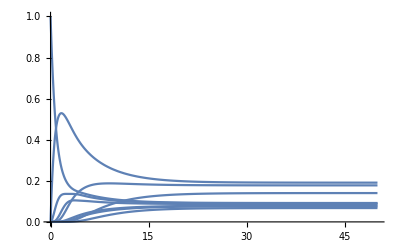

```mathematica
Plot[Table[ρ[i,i][t],{i,1,9}]/.sol1,{t,0,50},PlotRange-> All]
```

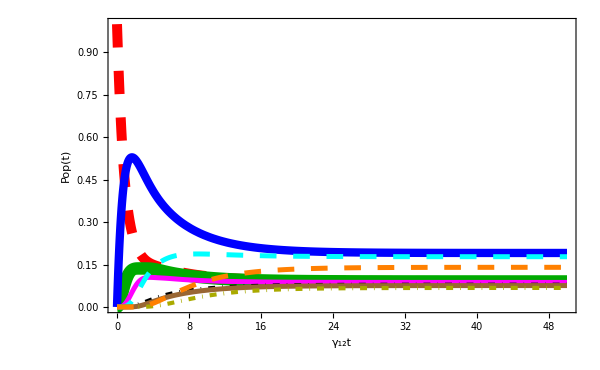

```mathematica
ShowLegend[Plot[{ρ[1,1][t]/.sol1,ρ[2,2][t]/.sol1,ρ[3,3][t]/.sol1,ρ[4,4][t]/.sol1,ρ[5,5][t]/.sol1,ρ[6,6][t]/.sol1,ρ[7,7][t]/.sol1,ρ[8,8][t]/.sol1,ρ[9,9][t]/.sol1},{t,0,50},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]},{Darker[Green],Thickness[0.015],CapForm["Round"],Dashing[{1*^-10,0.014 2,0.014 2,0.014 2}]},{Thickness[0.01],Blue},{Thickness[0.006],Magenta},{Thickness[0.005],DotDashed,Black},{Dashing[0.02],Thickness[0.006],Cyan},{Thickness[0.006],Brown},{Thickness[0.005],DotDashed,Darker[Yellow]},{Dashing[0.02],Thickness[0.006],Orange}},Frame->True,FrameLabel->{"γ_12t","Pop(t)"},FrameStyle->Directive[Black, AbsoluteThickness[1.5]],BaseStyle->{FontWeight->"Bold",FontSize->20},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->16]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]],Line[{{0,0.5},{4,0.5}}]}],Style["| 0_1, 1_2⟩",Bold,16]},
{Graphics[{Darker[Green],Thickness[0.1],CapForm["Round"],Dashing[{1*^-10,0.014 10,0.014 10,0.014 10}],Line[{{0,0.5},{4,0.5}}]}],Style["| 0_1, 2_2⟩",Bold,16]},{Graphics[{Blue,AbsoluteThickness[5],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 0_1, 3_2⟩",Bold,16]},{Graphics[{Magenta,AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 1_1, 1_2⟩",Bold,16]},{Graphics[{Black, DotDashed,AbsoluteThickness[2],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 1_1, 2_2⟩",Bold,16]},{Graphics[{Cyan,Dashing[0.2],AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 1_1, 3_2⟩",Bold,16]},{Graphics[{Brown,AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 2_1, 1_2⟩",Bold,16]},{Graphics[{Darker[Yellow], DotDashed,AbsoluteThickness[2],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 2_1, 2_2⟩",Bold,16]},{Graphics[{Orange,Dashing[0.2],AbsoluteThickness[3],Line[{{0,0.5},{2.75,0.5}}]}],Style["| 2_1, 3_2⟩",Bold,16]}},LegendPosition->{-0.19,-0.13},LegendBackground->White,LegendBorder->Black,LegendShadow->None,LegendSize->{0.43,0.62},LegendTextSpace->1.2},{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 2",Bold,25]}},LegendPosition->{0.45,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.2,0.1},LegendTextSpace->50},{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["(b)",Bold,32]}},LegendPosition->{-0.65,0.37},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.2,0.1},LegendTextSpace->20}]
```

#### Plotting sum of diagonal elements to check the normalization as we’ll use it as the 37th equation in the steady-state solution (37th equation was needed)

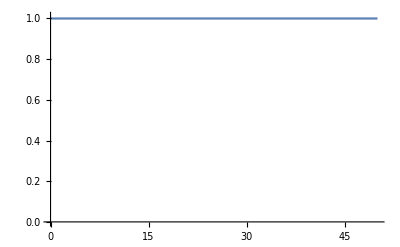

```mathematica
Plot[Sum[ρ[i,i][t],{i,1,9}]/.sol1,{t,0,50},PlotRange-> {{0,50},{0,1.01}}]
```

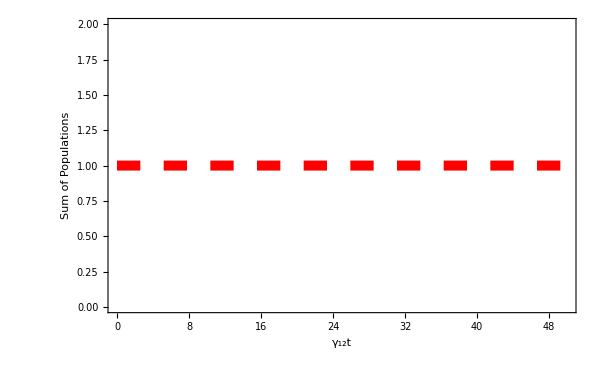

```mathematica
Plot[Sum[ρ[i,i][t],{i,1,9}]/.sol1,{t,0,50},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"γ_12t","Sum of Populations"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]]
```

## Steady-state Results

```mathematica
Clear[Γ,γ12,γ13,γ23,g,κ]
```

```mathematica
Set1=Table[Table[ρ[j,i]'[t]-> 0,{i,1,9}],{j,1,9}]//Flatten;
```

```mathematica
SSEquations1={Equations1/.Set1,1== Sum[ρ[i,i][t],{i,1,9}]}//Flatten;
```

```mathematica
Set2={Table[Table[ρ[j,i][t],{i,1,9}],{j,1,9}]}//Flatten;
```

```mathematica
SSsol1=Solve[SSEquations1,Set2]//Flatten;
```

```mathematica
Set3={Table[Table[ρss[j,i],{i,1,9}],{j,1,9}]}//Flatten;
```

```mathematica
{ρss[1,1],ρss[1,2],ρss[1,3],ρss[1,4],ρss[1,5],ρss[1,6],ρss[1,7],ρss[1,8],ρss[1,9],ρss[2,1],ρss[2,2],ρss[2,3],ρss[2,4],ρss[2,5],ρss[2,6],ρss[2,7],ρss[2,8],ρss[2,9],ρss[3,1],ρss[3,2],ρss[3,3],ρss[3,4],ρss[3,5],ρss[3,6],ρss[3,7],ρss[3,8],ρss[3,9],ρss[4,1],ρss[4,2],ρss[4,3],ρss[4,4],ρss[4,5],ρss[4,6],ρss[4,7],ρss[4,8],ρss[4,9],ρss[5,1],ρss[5,2],ρss[5,3],ρss[5,4],ρss[5,5],ρss[5,6],ρss[5,7],ρss[5,8],ρss[5,9],ρss[6,1],ρss[6,2],ρss[6,3],ρss[6,4],ρss[6,5],ρss[6,6],ρss[6,7],ρss[6,8],ρss[6,9],ρss[7,1],ρss[7,2],ρss[7,3],ρss[7,4],ρss[7,5],ρss[7,6],ρss[7,7],ρss[7,8],ρss[7,9],ρss[8,1],ρss[8,2],ρss[8,3],ρss[8,4],ρss[8,5],ρss[8,6],ρss[8,7],ρss[8,8],ρss[8,9],ρss[9,1],ρss[9,2],ρss[9,3],ρss[9,4],ρss[9,5],ρss[9,6],ρss[9,7],ρss[9,8],ρss[9,9]}=Table[SSsol1[[q,2]],{q,1,81}];
```

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

```mathematica
MeanPhoton0=Sum[Sum[n⟨Subscript[n, OverHat[1]],Subscript[i, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[i, OverHat[2]]⟩,{n,0,2}],{i,1,3}]/.Calling
```

ρ[4,4][t]+ρ[5,5][t]+ρ[6,6][t]+2 ρ[7,7][t]+2 ρ[8,8][t]+2 ρ[9,9][t]

```mathematica
MeanPhoton=Sum[ ρss[i,i],{i,4,6}]+Sum[ 2ρss[i,i],{i,7,9}]//Flatten;
```

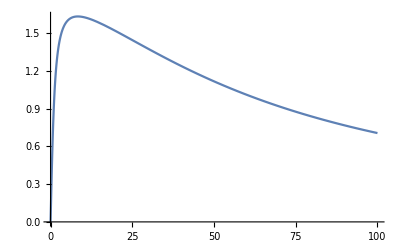

```mathematica
Plot[MeanPhoton/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,100},PlotRange->All]
```

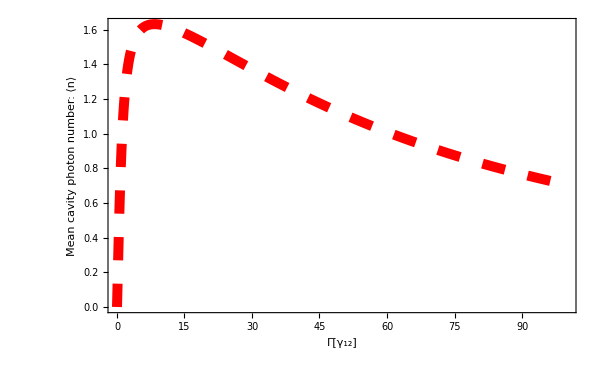

```mathematica
ShowLegend[Plot[MeanPhoton/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,100},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"Γ[γ_12]","Mean cavity photon number: ⟨n⟩"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 2",Bold,25]}},LegendPosition->{0.45,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.2,0.1},LegendTextSpace->50}]
```

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

```mathematica
Inversion0=Sum[⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩-⟨Subscript[n, OverHat[1]],Subscript[1, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[1, OverHat[2]]⟩,{n,0,2}]/.Calling
```

-ρ[1,1][t]+ρ[2,2][t]-ρ[4,4][t]+ρ[5,5][t]-ρ[7,7][t]+ρ[8,8][t]

```mathematica
Inversion=ρss[2,2]+ρss[5,5]+ρss[8,8]-ρss[1,1]-ρss[4,4]-ρss[7,7];
```

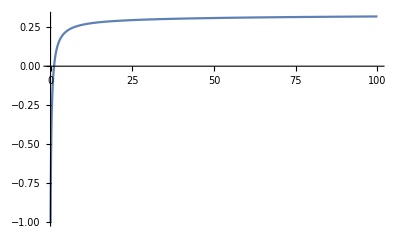

```mathematica
Plot[Inversion/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,100},PlotRange->All]
```

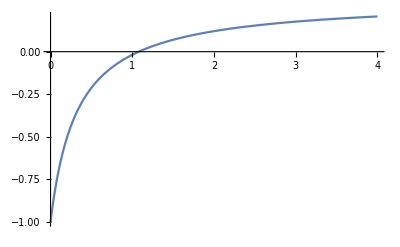

```mathematica
Plot[Inversion/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,4},PlotRange->All]
```

```mathematica
p1=ShowLegend[Plot[Inversion/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,100},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]}},Frame->True,FrameLabel->{"Γ[γ_12]","Inversion: Δ_12"},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 2",Bold,25]}},LegendPosition->{0.45,0.35},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.2,0.1},LegendTextSpace->50}];
```

```mathematica
p2=Plot[Inversion/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,4},PlotStyle-> {Thickness[0.017],Blue},Frame->True,FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.2]],BaseStyle->{FontWeight->"Bold",FontSize->18},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->10]];
```

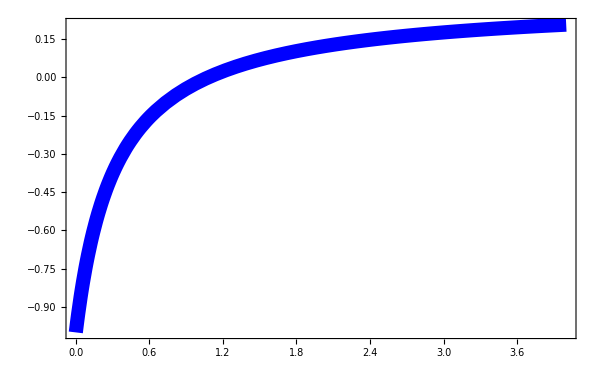

```mathematica
Show[Graphics[{Rectangle[{-7.2,-2.1},{8,9},p1],Rectangle[{0.5,0.5},{6.5,6.5},p2]}],ImageSize->{600,520}]
```

#### Plotting diagonal elements to see the behavior of populations and the steady-state time

```mathematica
G[n_]:=(4 g^2)/(γ12+Γ+2 κ (n-1/2-√(n(n+1))));
```

```mathematica
Rst0=Sum[G[n]n⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩,{n,0,2}]-Sum[G[n](n+1)⟨Subscript[n, OverHat[1]]+1,Subscript[1, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]]+1,Subscript[1, OverHat[2]]⟩,{n,0,1}]/.Calling
```

-(4 g^2 ρ[4,4][t])/(Γ+γ12-κ)+(4 g^2 ρ[5,5][t])/(Γ+γ12+2 (1/2-√2) κ)-(8 g^2 ρ[7,7][t])/(Γ+γ12+2 (1/2-√2) κ)+(8 g^2 ρ[8,8][t])/(Γ+γ12+2 (3/2-√6) κ)

```mathematica
Rst=-(G[0]) ρss[4,4]+(G[1]) ρss[5,5]-(G[1]) 2 ρss[7,7]+(G[2]) 2 ρss[8,8];
```

```mathematica
Rsp0=Sum[G[n]⟨Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]|·ρ̂[t]·|Subscript[n, OverHat[1]],Subscript[2, OverHat[2]]⟩,{n,0,2}]/.Calling
```

(4 g^2 ρ[2,2][t])/(Γ+γ12-κ)+(4 g^2 ρ[5,5][t])/(Γ+γ12+2 (1/2-√2) κ)+(4 g^2 ρ[8,8][t])/(Γ+γ12+2 (3/2-√6) κ)

```mathematica
Rsp=(G[0]) ρss[2,2]+(G[1]) ρss[5,5]+(G[2]) ρss[8,8];
```

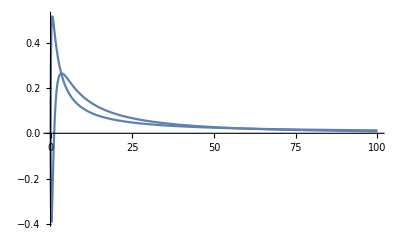

```mathematica
Plot[{Rst,Rsp}/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,100},PlotRange->All]
```

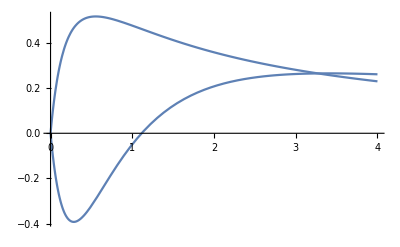

```mathematica
Plot[{Rst,Rsp}/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},{Γ,0,4},PlotRange->All]
```

```mathematica
p3=ShowLegend[Plot[{Rst/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},Rsp/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01}},{Γ,0,100},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.012]]},{Thickness[0.007],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","Rates"},FrameStyle->Directive[Black, AbsoluteThickness[1.5]],BaseStyle->{FontWeight->"Bold",FontSize->20},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->16]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]],Line[{{0,0.5},{4,0.5}}]}],Style["Stimulated",Bold,12]},
{Graphics[{Blue,Thickness[0.07],CapForm["Round"],Line[{{0,0.5},{4,0.5}}]}],Style["Spontaneous",Bold,12]}},LegendPosition->{-0.6,0.32},LegendBackground->White,LegendBorder->Black,LegendShadow->None,LegendSize->{0.52,0.15},LegendTextSpace->1.5},{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]]}],Style["n = 2",Bold,25]}},LegendPosition->{0.45,-0.25},LegendBackground->White,LegendBorder->None,LegendShadow->None,LegendSize->{0.2,0.1},LegendTextSpace->50}];
```

```mathematica
p4=Plot[{Rst/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01},Rsp/.{γ12-> 1,γ13-> 0,γ23-> 0.5,g-> 1,κ-> 0.01}},{Γ,0,4},PlotStyle-> {{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.016]]},{Thickness[0.016],Blue}},Frame->True,FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.5]],BaseStyle->{FontWeight->"Bold",FontSize->20},PlotRange->All,ImageSize->{600,500},PlotLabel->Style["",FontSize->16]];
```

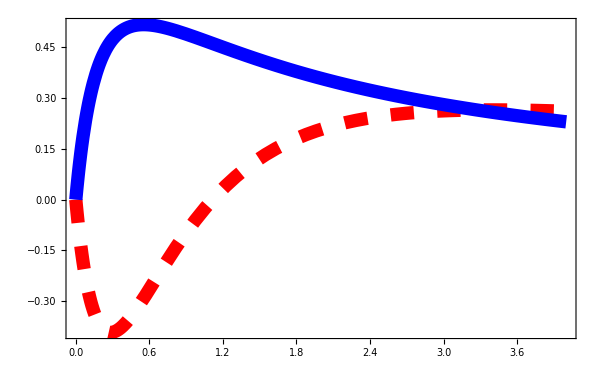

```mathematica
Show[Graphics[{Rectangle[{-7,-4.5},{9,9},p3],Rectangle[{0.3,0.3},{6.5,6.5},p4]}],ImageSize->{600,520}]
```